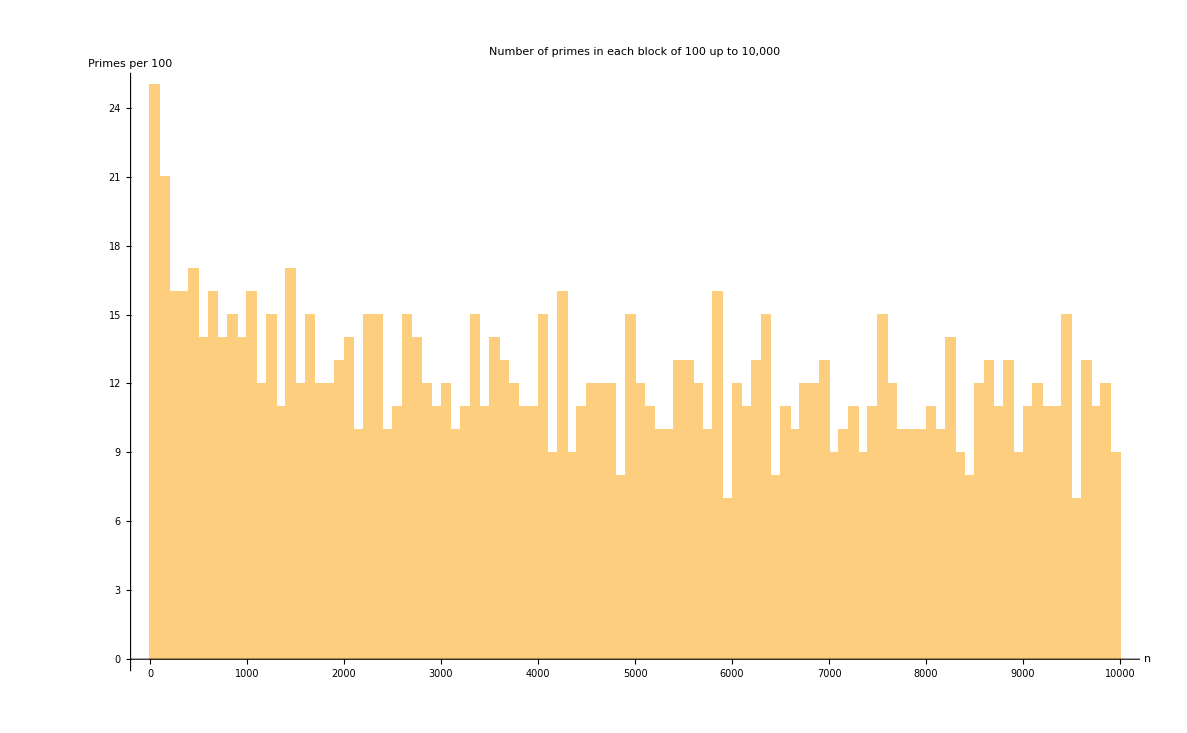

```mathematica
primes=Prime[Range[PrimePi[10000]]];

Histogram[primes,{0,10000,100},AxesLabel->{"n","Primes per 100"},PlotLabel->"Number of primes in each block of 100 up to 10,000",Ticks->{Range[0,10000,1000],Automatic},ImageSize->Large]
```

```mathematica
estimate=Table[{100 k-50,N[LogIntegral[100 k]-LogIntegral[Max[100 (k-1),2]]]},{k,1,100}];

Show[Histogram[primes,{0,10000,100},Ticks->{Range[0,10000,1000],Automatic}],ListLinePlot[estimate,PlotStyle->{Red,Thick}],ImageSize->Large]
```